```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/sec_int_data/500nm.dat"]
```

{{1.63065,0.190786},{1.58758,0.196717},{1.51023,0.218895},{1.46132,0.23246},{1.41705,0.246548},{1.38078,0.256888},{1.34407,0.264285},{1.30453,0.268499},{1.27782,0.272771},{1.24828,0.277404},{1.22646,0.285254},{1.20042,0.291325},{1.183,0.301067},{1.16401,0.29349},{1.14739,0.294236},{1.13423,0.29632},{1.12389,0.291848},{1.11401,0.101112},{1.10574,0.274825},{1.09905,0.252547},{1.09389,0.246313},{1.08918,0.27854},{1.08895,0.286757},{1.08874,0.289231},{1.08738,0.30358},{1.08767,0.314811},{1.08994,0.303211},{1.0948,0.314738},{1.10288,0.319326},{1.1168,0.321359},{1.12832,0.286757},{1.1517,0.317289},{1.18117,0.302324},{1.20042,0.301437},{1.25083,0.300327},{1.28067,0.283523},{1.3108,0.28983},{1.33715,0.274521}}

0.452837-0.145702 x

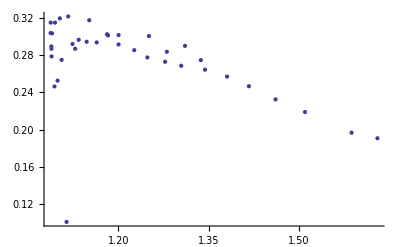

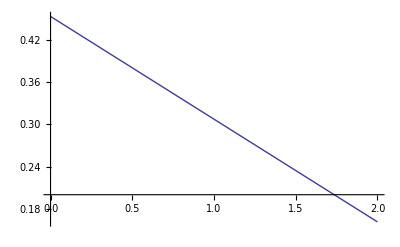

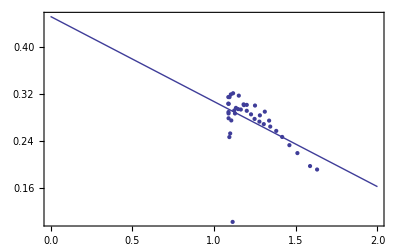

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```